# Cavity QED Systems: Spectral Properties

This material accompanies the Q3 Video Tutorial Episode 25.

-Graphics-

Figure 1: Originally, a cavity-QED system was a system of atoms interacting with quantized light in the cavity.

Two-level systems (atoms) are described by Qubits, denoted by symbol S.

```mathematica
Let[Qubit,S]
```

```mathematica
Dimension[S]
```

2

Bosonic modes (cavity photons) are described by Bosons, denoted by symbol c.

```mathematica
Let[Boson,c]
```

```mathematica
{Bottom[c],Top[c],Dimension[c]}
```

{0,5,6}

## Jaynes-Cummings Hamiltonian

The qubit has transition frequence Ω.

```mathematica
Let[Real,Ω]
Hq=(Ω/2)S[3]
```

(Ω S^z)/2

The photon has frequency ω.

```mathematica
Let[Real,ω]
Hc=ω*Dagger[c]**c
```

ω c^†c

The qubit-photon coupling in the rotating-wave approximation (RWA).

```mathematica
Let[Real,g]
Hg=g*(S[4]**c+Dagger[c]**S[5])
```

g (cS^++c^†S^-)

Construct the total Hamiltonian.

```mathematica
HH=Hq+Hc+Hg
```

ω c^†c+g (cS^++c^†S^-)+(Ω S^z)/2

### Basic Method

Examine the matrix representation of the Hamiltonian.

```mathematica
mat=Matrix[HH,{c,S}];
mat//MatrixForm
```

(Ω/2 | 0 | 0 | g | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -Ω/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ω+Ω/2 | 0 | 0 | √2 g | 0 | 0 | 0 | 0 | 0 | 0
g | 0 | 0 | ω-Ω/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 ω+Ω/2 | 0 | 0 | √3 g | 0 | 0 | 0 | 0
0 | 0 | √2 g | 0 | 0 | 2 ω-Ω/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 3 ω+Ω/2 | 0 | 0 | 2 g | 0 | 0
0 | 0 | 0 | 0 | √3 g | 0 | 0 | 3 ω-Ω/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 ω+Ω/2 | 0 | 0 | √5 g
0 | 0 | 0 | 0 | 0 | 0 | 2 g | 0 | 0 | 4 ω-Ω/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 ω+Ω/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | √5 g | 0 | 0 | 5 ω-Ω/2)

Write a small utility function to use to investigate the spectrum of the Hamiltonian.

```mathematica
spectrum[gv_]:=Block[
{ω=1,
Ω=1.05,
g},
g=gv;
val=Sort@Eigenvalues[Normal@mat]
]
```

Now, examine the level structure of the Hamiltonian and its evolution as coupling g varies.

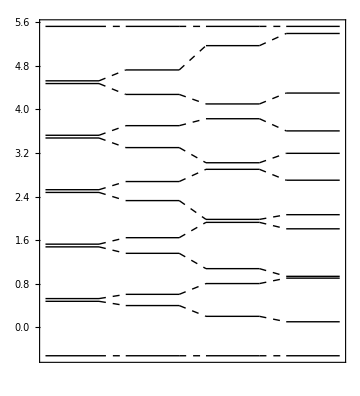

```mathematica
LevelsPlot[{spectrum[0.],spectrum[0.1],spectrum[0.3],spectrum[0.4]},ImageSize->Medium]
```

Note that there seems to be crossing of energy levels. Let us examine the spectrum more closely by varying g continuously.

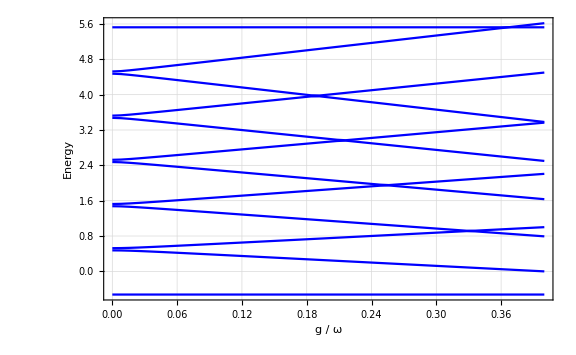

```mathematica
data=Transpose@Table[spectrum[x],{x,0,0.5,0.01}];
ListPlot[data,
FrameLabel->{"g / ω","Energy"},
Joined->True,DataRange->{0,0.4},PlotStyle->Blue]
```

## Parity Conservation

The numerical results above suggest that energy levels cross each other. This is unusual unless there is a symmetry.

Question: Is there a symmetry? What is it if any?

Indeed, the parity is conserved.

```mathematica
op=Parity[{c,S}]
```

Parity[c]S^z

```mathematica
op**HH-HH**op
```

0

Then, let us take a look at the basis again.

```mathematica
bs=Basis[{c,S}]
```

{0_c0_S,0_c1_S,1_c0_S,1_c1_S,2_c0_S,2_c1_S,3_c0_S,3_c1_S,4_c0_S,4_c1_S,5_c0_S,5_c1_S}

Note that each basis state is an eigenstate of the parity operator, each with different parities.

```mathematica
op**bs
```

{0_c0_S,-0_c1_S,-1_c0_S,1_c1_S,2_c0_S,-2_c1_S,-3_c0_S,3_c1_S,4_c0_S,-4_c1_S,-5_c0_S,5_c1_S}

Let us group the basis elements according to their parities.

```mathematica
ps=GroupBy[bs,ParityValue[{c,S}]]
```

<|1→{0_c0_S,1_c1_S,2_c0_S,3_c1_S,4_c0_S,5_c1_S},-1→{0_c1_S,1_c0_S,2_c1_S,3_c0_S,4_c1_S,5_c0_S}|>

Rearrange the basis so that basis states of the same parity come together, and then examine again the matrix.

```mathematica
bb=Catenate[ps];
new=MatrixIn[HH,bb];
new//MatrixForm
```

(Ω/2 | g | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
g | ω-Ω/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 (4 ω+Ω) | √3 g | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | √3 g | 3 ω-Ω/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 (8 ω+Ω) | √5 g | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | √5 g | 5 ω-Ω/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -Ω/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ω+Ω/2 | √2 g | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | √2 g | 2 ω-Ω/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (6 ω+Ω) | 2 g | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 g | 4 ω-Ω/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 ω+Ω/2)

The resulting matrix is indeed block diagonal!

Therefore, it is more efficient to handle each block separately.

```mathematica
mm=MatrixIn[HH,ps];
MatrixForm/@mm
```

<|1→(Ω/2 | g | 0 | 0 | 0 | 0
g | ω-Ω/2 | 0 | 0 | 0 | 0
0 | 0 | 1/2 (4 ω+Ω) | √3 g | 0 | 0
0 | 0 | √3 g | 3 ω-Ω/2 | 0 | 0
0 | 0 | 0 | 0 | 1/2 (8 ω+Ω) | √5 g
0 | 0 | 0 | 0 | √5 g | 5 ω-Ω/2),-1→(-Ω/2 | 0 | 0 | 0 | 0 | 0
0 | ω+Ω/2 | √2 g | 0 | 0 | 0
0 | √2 g | 2 ω-Ω/2 | 0 | 0 | 0
0 | 0 | 0 | 1/2 (6 ω+Ω) | 2 g | 0
0 | 0 | 0 | 2 g | 4 ω-Ω/2 | 0
0 | 0 | 0 | 0 | 0 | 5 ω+Ω/2)|>

## Summary

### Functions

LevelsPlot

Sort

Parity, ParityValue

MatrixIn

Qubit, Dimension

Boson, Bottom, Top, Dimension

Matrix, ExpressionFor

ProperValues, ProperStates, ProperSystem

### Related Links

Mahn-Soo Choi, Advanced Quantum Technologies 12, 2000085 (2020), “Exotic Quantum States of Circuit Quantum Electrodynamics in the Ultra-Strong Coupling Regime.”

C. Dongni, S. Luo, Y.-D. Wang, S. Chesi, and Mahn-Soo Choi, Physical Review A 105, 022627 (2022), “Geometric manipulation of a decoherence-free subspace in atomic ensembles.”

## Epilog

```mathematica
WorkHere[]
```

/Users/Masso/Math/Apples/QuantumPlaybook/YouTube2023b

```mathematica
<<PlaybookTools`
```

```mathematica
PlaybookDeploy[NotebookFileName[],"InVideos",
"PrintHandout"->True,
"DeleteOutput"->True,
"FoldSections"->True]
```

Deploying /Users/Masso/Math/Apples/QuantumPlaybook/YouTube2023b/31_Simon.nb

Copying to /Users/Masso/Math/Apples/QuantumPlaybook/YouTube2023b/InVideos/31_Simon.Playbook.nb

Examining {} for deletion.

Deleting {,,,,,,,,,,,,,,,}

Deleting Cells of style Output

Closing Cells of style Subsubsection

Closing Cells of style Subsection

Closing Cells of style Section

Saving /Users/Masso/Math/Apples/QuantumPlaybook/YouTube2023b/InVideos/31_Simon.Playbook.nb

```mathematica
SystemOpen[ExpandFileName@"InVideos"]
```